```mathematica
(*HIGH DEGREE MATRIX*)
HDMatrix[d_,k_]:=Module[{A = ConstantArray[0,{d-(k-2),d-(k-2)}],B=0,AHD=0},
If[d≠k,
A[[2;;,2;;]]= DiagonalMatrix[Range[-k,-d,-1]]+DiagonalMatrix[Range[k,d-1,1],1];
A [[1,1]] = -1;
A [[1,2]] = k-1;
,
A = {{-1,k-1},{0,-k}}
];
(*HD Removal*)
B = ConstantArray[0,{d-(k-2),d-(k-2)}];
B[[d-(k-2),;;]] = -1;
AHD= d/1*(A+B)
]

(*TRIMMING MATRIX*)
ChoppingMatrix[d_,k_]:=Module[{A = ConstantArray[0,{d-(k-2),d-(k-2)}],B=0,AK=0},
If[d≠k,
A[[2;;,2;;]]= DiagonalMatrix[Range[-k,-d,-1]]+DiagonalMatrix[Range[k,d-1,1],1];
A [[1,1]] = -1;
A [[1,2]] = k-1;
,
A = {{-1,k-1},{0,-k}}
];
(*TRIMMING*)
B = ConstantArray[0,{d-(k-2),d-(k-2)}];
B[[1,;;]] = -1;
AK=1/1*(A+B)
]

(*Projection and Lifting Operators*)
Project[d_,k_]:=Module[{L =ConstantArray[0,{d,d-(k-2)}],P=0},
(*Lifting*)
L[[1;;k-2,1]] = 1;
L[[k-1;;,;;]] = ReplacePart[L[[k-1;;,;;]],{i_,i_}->1];
(*Projecting*)
P = Transpose[L]
]


(*INFINITISSIMAL OPERATORS*)
T[dt_,t0_,d_,k_,A_,α_]:=(IdentityMatrix[d-(k-2)]+dt/(1-α*t0)*A);
TN[dt_,t0_,d_,k_,A_]:=(IdentityMatrix[d-(k-2)]+dt/(1-t0)*A);
(*
THD[dt_,t0_,d_,k_]:=(IdentityMatrix[d]+dt/(1-d*t0)*AHD);
TK[dt_,t0_,d_,k_]:=(IdentityMatrix[d-(k-2)]+dt/(1-t0)*AK);
*)
```

## HIGH DEGREE WITH CHOPPING

OPERATOR LIMIT

```mathematica
Evolution[X0_,t0_,dt_,tin_,d_,k_]:=Module[{ans=0,Timeline = {},Zeit = {},X = N[X0],t=t0,ddt = 0,AK=ChoppingMatrix[d,k],AHD=HDMatrix[d,k],tout=tin,out={},temp=0,tol=10^(-10),done=0},

While[Last[X][[1]]>0,
temp+=1;
(*Check for Transition*)
If[(AK.X)[[1,1]]≥-tol,done=1;Break[],Indeterminate];

(*Chopping Part*)
ddt = (1-t)*(-X[[1,1]]/(AK.X)[[1,1]]);
tout+=ddt*Apply[Plus,X0][[1]];
X = TN[ddt,t,d,k,AK].X;

t = t+2*ddt;

AppendTo[Zeit,tout];
AppendTo[Timeline,X//N];



(*HD Part*)
X = TN[dt,t,d,k,AHD].X;
t = t+2*d*dt;
tout += dt*Apply[Plus,X0][[1]];

AppendTo[Zeit,tout];
AppendTo[Timeline,X//N];

ans +=dt;

(*Some Output*)
AppendTo[out,ddt/(1-t)];

];

{X,tout,Timeline,Zeit,ans,out,done}
]

OperatorTimeline[dt_,d_,k_]:=Module[{X0 = ConstantArray[0,{d,1}], ts=0,tLine={},fraction=0,counter={},norm={},stopTime={},tLineOut={},additionalOut={}, XIn=0,XOut=0,Timeline=0,Zeit=0,ans=0,out=0,dCur=d,dummy = {},temp=0,done=0},

(*Initialization*)
X0[[d,1]]=d;
X0 = Project[d,k].X0;
tLine={{0,Table[X0[[i,1]]/(i+(k-2)),{i,1,Length[X0]}]}};

(*Evolution*)
XIn = N[X0];

For[dCur=d,dCur≥k,dCur--,
PrintTemporary[dCur];
{XOut,ts,Timeline,Zeit,ans,out,done} = Evolution[N[XIn],0,dt,ts,dCur,k];

(*Save output*)
AppendTo[stopTime,{dCur,ts}];
AppendTo[counter,{dCur,ans}];
AppendTo[norm,{dCur,Apply[Plus,XIn][[1]]}];
fraction += ans*Apply[Plus,XIn][[1]];
AppendTo[additionalOut,{dCur,out}];

tLineOut =Table[{Zeit[[i]], Table[If[deh<=Length[XOut],Timeline[[i]][[deh,1]]/(deh+(k-2)),0],{deh,1,d-(k-2)}]},{i,1,Length[Timeline]}];
AppendTo[dummy,{dCur,tLineOut}];
tLine=Catenate[{tLine,tLineOut}];

XIn = XOut[[1;;Length[XOut]-1]];

(*Check for transition. If yes: done*)
If[done==1,Break[]]

];


{tLine,fraction,stopTime,counter,norm,additionalOut,dummy}

]
```

```mathematica
(*Run Operator Limit*)
dt=10^(-5);
d = 7;
k = 3;
{tLine,fraction,stopTime,counter,norm,additionalOut,test} = OperatorTimeline[dt,d,k];
fraction
```

0.337671

```mathematica
fraction (*-7*)
```

0.250002

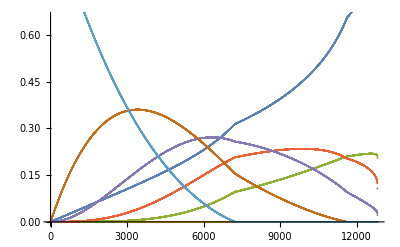

```mathematica
totalTimeline = Table[Flatten[tLine[[i]]],{i,1,Length[tLine]}];
ListPlot[Transpose[totalTimeline]]
```

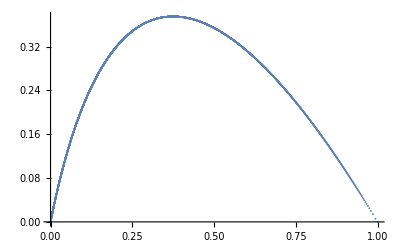

```mathematica
ListPlot[Table[{xData[[1]][[i]],yData[[2]][[i]]},{i,1,Length[totalTimeline]}]]
```

```mathematica
totalTimeline = Table[Flatten[tLine[[i]]],{i,1,Length[tLine]}];
(*Export Results*)
xData = {Table[totalTimeline[[i,1]],{i,1,Length[totalTimeline]}]};
yData = Table[Table[totalTimeline[[i,j]],{i,1,Length[totalTimeline]}],{j,2,Length[totalTimeline[[1]]-1]}];

Export["~/Dropbox/Promotion/work/k core/div/operator_limit/data/"<>"xData_"<>ToString[d]<>ToString[k]<>".dat",xData,"Table","FieldSeparators"->","]
Export["~/Dropbox/Promotion/work/k core/div/operator_limit/data/"<>"yData_"<>ToString[d]<>ToString[k]<>".dat",yData,"Table","FieldSeparators"->","]


Export["~/Dropbox/Promotion/work/k core/div/operator_limit/data/"<>"Data_"<>ToString[d]<>ToString[k]<>".dat",totalTimeline,"Table","FieldSeparators"->","]
```

~/Dropbox/Promotion/work/k core/div/operator_limit/data/xData_73.dat

~/Dropbox/Promotion/work/k core/div/operator_limit/data/yData_73.dat

~/Dropbox/Promotion/work/k core/div/operator_limit/data/Data_73.dat

```mathematica
totalTimeline = Table[Flatten[tLine[[i]]],{i,1,Length[tLine]}];
totalTimeline[[1;;100]]//Grid
```

0 | 0 | 0 | 1
0. | 0. | 0. | 1.
0.00003 | 0. | 0.00009 | 0.99988
0.00003 | 0. | 0.00009 | 0.99988
0.00006 | 5.40032×10^-9 | 0.000179989 | 0.99976
0.0000600054 | 8.27181×10^-25 | 0.000179995 | 0.99976
0.0000900054 | 1.0801×10^-8 | 0.000269973 | 0.99964
0.0000900162 | 0. | 0.000269984 | 0.99964
0.000120016 | 1.62019×10^-8 | 0.000359951 | 0.99952
0.000120032 | 3.30872×10^-24 | 0.000359968 | 0.99952
0.000150032 | 2.16032×10^-8 | 0.000449924 | 0.9994
0.000150054 | -3.30872×10^-24 | 0.000449946 | 0.9994
0.000180054 | 2.70049×10^-8 | 0.000539892 | 0.99928
0.000180081 | -6.61744×10^-24 | 0.000539919 | 0.99928
0.000210081 | 3.24068×10^-8 | 0.000629854 | 0.99916
0.000210113 | 0. | 0.000629887 | 0.99916
0.000240113 | 3.78091×10^-8 | 0.000719811 | 0.99904
0.000240151 | -6.61744×10^-24 | 0.000719849 | 0.99904
0.000270151 | 4.32117×10^-8 | 0.000809762 | 0.99892
0.000270195 | 6.61744×10^-24 | 0.000809805 | 0.99892
0.000300195 | 4.86146×10^-8 | 0.000899708 | 0.9988
0.000300243 | -6.61744×10^-24 | 0.000899757 | 0.9988
0.000330243 | 5.40178×10^-8 | 0.000989649 | 0.99868
0.000330297 | 6.61744×10^-24 | 0.000989703 | 0.99868
0.000360297 | 5.94214×10^-8 | 0.00107958 | 0.99856
0.000360357 | 6.61744×10^-24 | 0.00107964 | 0.99856
0.000390357 | 6.48253×10^-8 | 0.00116951 | 0.99844
0.000390422 | 1.32349×10^-23 | 0.00116958 | 0.99844
0.000420422 | 7.02295×10^-8 | 0.00125944 | 0.99832
0.000420492 | 1.32349×10^-23 | 0.00125951 | 0.99832
0.000450492 | 7.5634×10^-8 | 0.00134936 | 0.9982
0.000450568 | 0. | 0.00134943 | 0.9982
0.000480568 | 8.10389×10^-8 | 0.00143927 | 0.99808
0.000480649 | 0. | 0.00143935 | 0.99808
0.000510649 | 8.64441×10^-8 | 0.00152918 | 0.99796
0.000510735 | 0. | 0.00152926 | 0.99796
0.000540735 | 9.18496×10^-8 | 0.00161908 | 0.99784
0.000540827 | 0. | 0.00161917 | 0.99784
0.000570827 | 9.72555×10^-8 | 0.00170898 | 0.99772
0.000570925 | 0. | 0.00170908 | 0.99772
0.000600925 | 1.02662×10^-7 | 0.00179887 | 0.9976
0.000601027 | 0. | 0.00179897 | 0.9976
0.000631027 | 1.08068×10^-7 | 0.00188876 | 0.99748
0.000631135 | 0. | 0.00188886 | 0.99748
0.000661135 | 1.13475×10^-7 | 0.00197864 | 0.99736
0.000661249 | 0. | 0.00197875 | 0.99736
0.000691249 | 1.18882×10^-7 | 0.00206851 | 0.99724
0.000691368 | 1.32349×10^-23 | 0.00206863 | 0.99724
0.000721368 | 1.2429×10^-7 | 0.00215838 | 0.99712
0.000721493 | -2.64698×10^-23 | 0.00215851 | 0.99712
0.000751493 | 1.29697×10^-7 | 0.00224825 | 0.997
0.000751623 | -2.64698×10^-23 | 0.00224838 | 0.997
0.000781623 | 1.35105×10^-7 | 0.00233811 | 0.99688
0.000781758 | -2.64698×10^-23 | 0.00233824 | 0.99688
0.000811758 | 1.40514×10^-7 | 0.00242796 | 0.99676
0.000811899 | 0. | 0.0024281 | 0.99676
0.000841899 | 1.45923×10^-7 | 0.00251781 | 0.99664
0.000842045 | 2.64698×10^-23 | 0.00251796 | 0.99664
0.000872045 | 1.51332×10^-7 | 0.00260765 | 0.99652
0.000872196 | 0. | 0.0026078 | 0.99652
0.000902196 | 1.56741×10^-7 | 0.00269749 | 0.9964
0.000902353 | 0. | 0.00269765 | 0.9964
0.000932353 | 1.62151×10^-7 | 0.00278732 | 0.99628
0.000932516 | -2.64698×10^-23 | 0.00278748 | 0.99628
0.000962516 | 1.67561×10^-7 | 0.00287715 | 0.99616
0.000962684 | 0. | 0.00287732 | 0.99616
0.000992684 | 1.72971×10^-7 | 0.00296697 | 0.99604
0.000992857 | 2.64698×10^-23 | 0.00296714 | 0.99604
0.00102286 | 1.78382×10^-7 | 0.00305679 | 0.99592
0.00102304 | 0. | 0.00305696 | 0.99592
0.00105304 | 1.83793×10^-7 | 0.0031466 | 0.9958
0.00105322 | 0. | 0.00314678 | 0.9958
0.00108322 | 1.89205×10^-7 | 0.0032364 | 0.99568
0.00108341 | 0. | 0.00323659 | 0.99568
0.00111341 | 1.94616×10^-7 | 0.0033262 | 0.99556
0.0011136 | -2.64698×10^-23 | 0.0033264 | 0.99556
0.0011436 | 2.00028×10^-7 | 0.003416 | 0.99544
0.00114381 | -2.64698×10^-23 | 0.00341619 | 0.99544
0.00117381 | 2.05441×10^-7 | 0.00350578 | 0.99532
0.00117401 | 0. | 0.00350599 | 0.99532
0.00120401 | 2.10853×10^-7 | 0.00359557 | 0.9952
0.00120422 | -5.29396×10^-23 | 0.00359578 | 0.9952
0.00123422 | 2.16266×10^-7 | 0.00368535 | 0.99508
0.00123444 | 2.64698×10^-23 | 0.00368556 | 0.99508
0.00126444 | 2.2168×10^-7 | 0.00377512 | 0.99496
0.00126466 | 2.64698×10^-23 | 0.00377534 | 0.99496
0.00129466 | 2.27093×10^-7 | 0.00386488 | 0.99484
0.00129489 | 2.64698×10^-23 | 0.00386511 | 0.99484
0.00132489 | 2.32507×10^-7 | 0.00395465 | 0.99472
0.00132512 | 0. | 0.00395488 | 0.99472
0.00135512 | 2.37922×10^-7 | 0.0040444 | 0.9946
0.00135536 | 0. | 0.00404464 | 0.9946
0.00138536 | 2.43336×10^-7 | 0.00413415 | 0.99448
0.0013856 | 1.05879×10^-22 | 0.0041344 | 0.99448
0.0014156 | 2.48751×10^-7 | 0.0042239 | 0.99436
0.00141585 | 5.29396×10^-23 | 0.00422415 | 0.99436
0.00144585 | 2.54166×10^-7 | 0.00431364 | 0.99424
0.00144611 | -5.29396×10^-23 | 0.00431389 | 0.99424
0.00147611 | 2.59582×10^-7 | 0.00440337 | 0.99412
0.00147637 | 0. | 0.00440363 | 0.99412